### Solve differential equations of population growth

#### Set constants

```mathematica
ClearAll[S0,R0,K,S,R,s,r,t,α,μ1,μ2]
S0=1*^3;
R0=0*^3;
P0=1*^2;
K=1*^4;
d=0.3;
tmax=20;
```

#### Population growth equations - simple

```mathematica
(*solution = DSolve[{
S'[t]==μ1*S[t]-α*S[t],
R'[t]==μ2*R[t]+α*S[t]
},{S[t],R[t]},t];*)
```

#### Population growth equations - logistic growth

```mathematica
solution = ParametricNDSolve[{
S'[t]==μ1*(1-((S[t]+R[t])/K))*S[t]-α*S[t],
R'[t]==μ2*(1-((S[t]+R[t])/K))*R[t]+α*S[t]-d*R[t],
WhenEvent[S[t]==1,S[t]->0],
S[0]==S0,R[0]==R0},
{S,R},
{t,0,tmax},
{μ1,μ2,α}];
```

```mathematica
solution = ParametricNDSolve[{
S'[t]==μ1*(1-((S[t]+R[t])/K))*S[t]-α*(P[t]/P0)*S[t],
R'[t]==μ2*(1-((S[t]+R[t])/K))*R[t]+α*(P[t]/P0)*S[t]-d*R[t],
P'[t]==-α*P[t](*+d*R[t]*),
WhenEvent[S[t]==1,S[t]->0],
S[0]==S0,R[0]==R0,P[0]==P0},
{S,R,P},
{t,0,tmax},
{μ1,μ2,α}]
```

{S→ParametricFunction[<>],R→ParametricFunction[<>],P→ParametricFunction[<>]}

#### Assign equations to functions

```mathematica
s[t_]=S[t]/.solution
r[t_]=R[t]/.solution
```

ParametricFunction[<>][t]

ParametricFunction[<>][t]

#### Plot

```mathematica
mu1={.8};
(*mu2={.75,.78};*)
mu2={.775}
alp={.1};
plotmax=tmax;

params=Join@@@Table[{m1/m2,α},{m1,mu1},{α,alp},{m2,mu2}];
```

{0.775}

```mathematica
(*DensityPlot[Log10[S[.8,.75,α][t]]/.solution,{t,0,100},{α,.1,.3}]*)
```

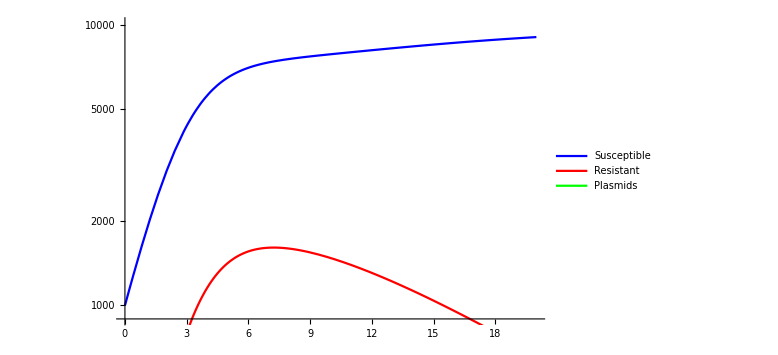

```mathematica
Show[LogPlot[
Evaluate@Table[S[μ1,μ2,α][t]/.solution,
{μ1,mu1},{α,alp},{μ2,mu2}],
{t,0,tmax},
PlotRange->All,
(*PlotRange-> {{0,plotmax},{0,5*^3}},*)
PlotStyle->{Thick, Blue},
PlotLegends->{"Susceptible"}
],

LogPlot[
Evaluate@Table[R[μ1,μ2,α][t]/.solution,
{μ1,mu1},{α,alp},{μ2,mu2}],
{t,0,tmax},
PlotStyle->{Thick, Red},
PlotRange->All,
PlotLegends->{"Resistant"}],

LogPlot[
Evaluate@Table[P[μ1,μ2,α][t]/.solution,
{μ1,mu1},{α,alp},{μ2,mu2}],
{t,0,tmax},
PlotStyle->{Green,Thick},
PlotRange->All,
PlotLegends->{"Plasmids"}
],

(*Plot[5,{t,0,plotmax},PlotStyle->Red],*)
ImageSize->Large]
```

```mathematica
(*Show[Plot[Evaluate@Table[{
Log[s[t,.8,μ2,α]],
Log[r[t,.8,μ2,α]]},
{μ2,{.75,.78}},{α,{.1,.3}}],
{t,1,20},
PlotLegends->{"S","R"},
AxesLabel->{{"t"},"Population"},
PlotStyle->Thick],ImageSize->Large]*)
```

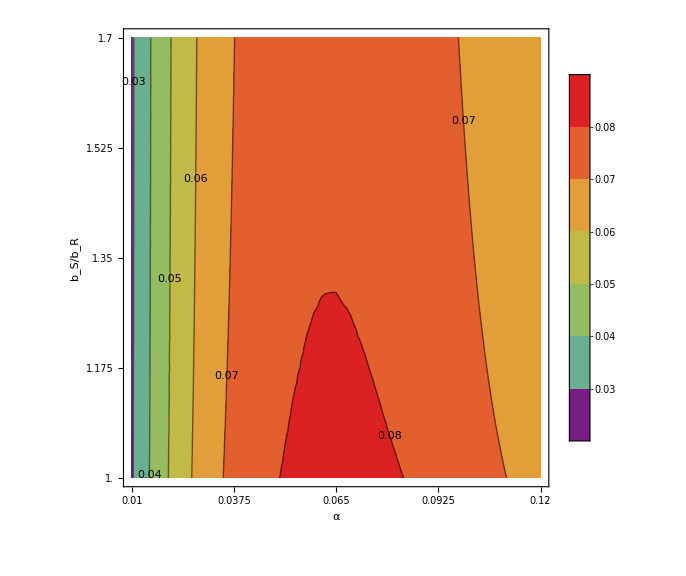

```mathematica
newStyle[x_]:=x/.l_Line:>Sequence[Opacity[1],Thick,Red,l];
r1=Range[-3,3,0.2];
r2=Range[-3,3,0.1];
tickfreq=0.05;
ticks[min_,max_]:=Table[With[{val=Round[Abs@FractionalPart[i],0.01]},Which[Chop[Min[Abs[r1-val]]]==0,{i,i,.06,Red},Chop[Min[Abs[r2-val]]]==0,{i,"",.04,Green},1<2,{i,"",.02,Blue}]],{i,Floor[min],Ceiling[max],tickfreq}]

ContourPlot[
R[μ1,1,α][tmax]/S[μ1,1,α][tmax]/.solution,
{α,.01,.12},{μ1,1,1.7},
ContourLabels->All,
FrameLabel->{"α","b_S/b_R"},
(*PlotLabel->"R/S Population",*)
PlotLegends->BarLegend[Automatic,LabelStyle->{FontSize->18}],
ColorFunction->"Rainbow",
BaseStyle->{FontWeight->"Normal", FontSize->18},
FrameTicks->{
{Subdivide[1,1.7,4],None},
{Subdivide[.01,.12,4],None}
},Axes->True,ImageSize->Large]/.
Tooltip[x_,1]:>Tooltip[newStyle[x],1]
```

```mathematica
Solve[{0 == Subscript[μ, s] S (1 - (S + R)/K) - α R, 
  0 == Subscript[μ, r]
      R (1 - (S + R)/K) + α R - δ R}, {S, R}]
```

{{S→0,R→0},{S→10000,R→0},{S→(10000 (α^2-α δ+α μ_r))/(α μ_r-α μ_s+δ μ_s),R→-(10000 (α-δ) (α-δ+μ_r) μ_s)/(μ_r (α μ_r-α μ_s+δ μ_s))}}

```mathematica
Range[1,6,3]
```

{1,4}